# Prva domača naloga 2025/26

## 1. Naloga

Seštej prvih 50 decimalk  števila . Rešitev zapiši v eni vrstici.

```mathematica
Total[RealDigits[N[356/745, 50]][[1]]]
```

257

## 2. Naloga

V spremenljivko `izraz` shrani izraz , v spremenljivko `izraz1` pa  .

FE`ExecuteInDynamicModule::novaldu: Symbol FE`DynamicModuleVariableList$36 does not have a value. Dynamic updating may be disabled.

a) Vse pojavitve parametra x v izrazu `izraz` zamenjaj z (x+1)^2. Dobljeni izraz shrani v `izraz2`.

b) Izračunaj vrednost `izraz`-`izraz1` in dobljeno število čim bolj poenostavi. Nato izračunaj numerično vrednost dobljenega števila na 15 decimalnih mest natančno.

c) Definiraj funkcijo , ki kot argument sprejme realno število  in vrne numerično vrednost `(izraz+izraz1)/izraz2` pri x=n. Izračunaj f(2).

d) Za funkcijo  iz dela c) poenostavi izraz  za x = 6, y = -1/2 in z = -1.

```mathematica
izraz = Log[10, E]/(Cos[Pi/4]^2) + (x+2)/10+x
izraz1 = Log[E]/Cos[Pi/4]^2 +(x+2)/10+x
izraz2 = izraz /. x->(x+1)^2
rez = Simplify[izraz - izraz1]
N[rez, 15]
f[n_]:=N[(izraz+izraz1)/izraz2 /. x -> n]
f[2]
Simplify[f[Log[3, (x^2-8x z+3y)]-(x-3)^2] /. {x->6, y->-1/2, z->-1}]
```

x+(2+x)/10+2/Log[10]

2+x+(2+x)/10

(1+x)^2+1/10 (2+(1+x)^2)+2/Log[10]

-2+2/Log[10]

-1.1314110361935

0.699141

-0.415436

## 3. Naloga

a) Napiši  funkcijo `vrednostSin`, ki  bo  sprejela  število `x`, izračunala numerično vrednost števila `sin(x)` in  rezultat  izpisala  v  obliki
“Numerična vrednost sin([x]) je enaka [numericna_vrednost].”,
kjer [x] nadomestiš z vnešeno vrednostjo, [numericna_vrednost] pa z numerično vrednostjo sinusa pri vnešenem x na 7 decimalk natančno. Izračunaj `vrednostSin[-π/4]`.

b) Definiraj anonimno funkcijo g (s parametrom #) s predpisom . Izračunaj g(6).

c) Definiraj seznam `sez` dolžine 9, katerega i-ti element je vrednost g(i+1), kjer je g funkcija iz b). Izračunaj povprečno vrednost vseh elementov v dobljenem seznamu. Nato ustvari seznam `sez1000` tako, da iz seznama `sez` izbereš le tiste elemente, ki so manjši  od 1000.

d) Pobriši vrednosti spremenljivk `g`, `sez` in `sez1000`. Nato napiši kodo v eni vrstici, ki bo vrnila seznam z enakimi elementi, kot v prejšnji nalogi `sez1000.b4. Pri tem ne definiraj nobenih novih spremenljivk.

e) Z uporabo funkcije `RecurrenceTable`izračunaj prvih 10 členov zaporedja  z začetnima členoma  . Nato določi po absolutni vrednosti največji element izmed dobljenih 10 členov zaporedja v primeru, ko je c = -2.

```mathematica
ClearAll[x]
vrednostSin[x_ ]:=Print["Numerična vrednost sin(",x,") je enaka ",NumberForm[N[Sin[x],7],{Infinity,7}]]
vrednostSin[-Pi/4]
ClearAll[x]
g[x_]:=x^4 - Exp[x]/(x^2-1)
g[6]
sez = Table[g[i+1], {i, 1, 9}]
Mean[sez]
sez1000=Select[sez,#<1000&]
Clear[g,sez,sez1000];
Select[Table[i^4-E^i/(i^2-1),{i,2,10}],#<1000&]
ClearAll[n, a]
Max[Abs[RecurrenceTable[{a[n]==(a[n-1]+a[n-2])/2,a[1]==-2,a[2]==-2/3},a,{n,1,10}]]]
```

Numerična vrednost sin(-π/4) je enaka -0.7071068

1296-ⅇ^6/35

{16-ⅇ^2/3,81-ⅇ^3/8,256-ⅇ^4/15,625-ⅇ^5/24,1296-ⅇ^6/35,2401-ⅇ^7/48,4096-ⅇ^8/63,6561-ⅇ^9/80,10000-ⅇ^10/99}

1/9 (25332-ⅇ^2/3-ⅇ^3/8-ⅇ^4/15-ⅇ^5/24-ⅇ^6/35-ⅇ^7/48-ⅇ^8/63-ⅇ^9/80-ⅇ^10/99)

{16-ⅇ^2/3,81-ⅇ^3/8,256-ⅇ^4/15,625-ⅇ^5/24}

{16-ⅇ^2/3,81-ⅇ^3/8,256-ⅇ^4/15,625-ⅇ^5/24}

2

## 4. Naloga

a) Definiraj funkciji  in . Nato nariši njuna grafa na intervalu [-2,2] v isti koordinatni sistem.

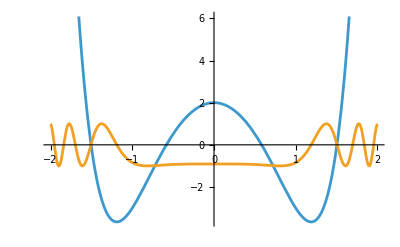

```mathematica
g[x_]:= x^6 -6 x^2 +2;
h[x_]:= Sin[x^4-2];
Plot[{g[x], h[x]}, {x, -2, 2}]
```

b) Nariši spodnjo sliko: zapolnjeni elipsi oranžne in zelene barve (prva  s središčem v (0,0), druga s središčem v (6,0), obe s polosema a=3,b=4) ter  rdeč krog s središčem v (3,0) in polmerom r=2.

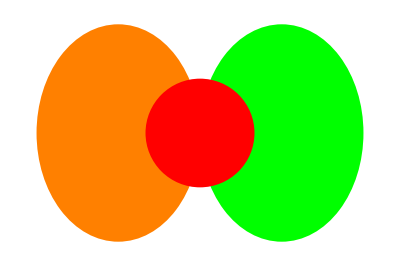

```mathematica
Graphics[{Orange,Disk[{0,0},{3,4}],Green,Disk[{6,0},{3,4}],Red,Disk[{3,0},2]}]
```

-Graphics-

c) Ponovno nariši zgornjo sliko, tokrat interaktivno tako, da se bo dalo rdečemu krogu spreminjati drugo koordinato središča na intervalu [-5,5]. Na sliki tudi označi vsa tri središča s črno točko.

```mathematica
Manipulate[Graphics[{Orange,Disk[{0,0},{3,4}],Green,Disk[{6,0},{3,4}],Red,Disk[{3,a},2],Black,PointSize[Small],Point[{0,0}],Point[{6,0}],Point[{3,a}]},PlotRange->{{-4,10},{-6,6}}],{a,-5,5}]
```

d) Napiši funkcijo `barve`, ki sprejme tri barve (barva1, barva2, barva3) in nariše sliko iz naloge b) tako, da je prva elipsa barve barva1, druga elipsa barve barva2 in krog barve barva3. (klic barve[Green,Purple,Yellow] naj vrne spodnjo sliko).

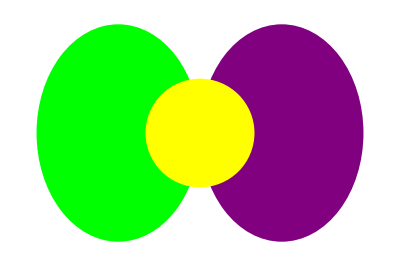

```mathematica
barve[barva1_,barva2_,barva3_]:=Graphics[{barva1,Disk[{0,0},{3,4}],barva2,Disk[{6,0},{3,4}],barva3,Disk[{3,0},2]}]
barve[Green, Purple, Yellow]
```

-Graphics-